# κτS^2

# Secondary structure (S^2)assignment to residues of proteins based on the curvature (κ) and torsion (τ) of the backbone.

## Read a list of PDB codes from the PDB repository and cure data to obtain: (i) the coordinates of the backbone atoms (of chain A) of the PDB, and (ii) the author’s secondary structure labeling.

### Reading the necessary information from the PDB repository

list[pdb] is the list of  PDB codes of the proteins. The set of proteins can be increased by adding new PDB codes at the end of this list.

```mathematica
list[pdb]={"8ABP","3C1A","2TSC","2CYP","2CCY","256B","1FXI","1GP1","1PRC","1A12","1B35","1C1D","1CFZ","1CKM","1COL","1DJ7","1EBF","1EI7","1EI9","1ETE","1FJR","1G31","1GD8","1GNW","1H21","1H6D","1HUL","1I2K","1I8N","1ID1","1JSS","1KNG","1KOL","1KWA","1LBQ","1LFW","1LJ2","1M4I","1MKF","1MSP","1MXR","1NH1","1NIJ","1O9Y","1OKC","1OR4","1OYG","1OZ2","1P4C","1PYA","1QEX","1QQR","1R89","1RJD","1RL6","1RYI","1S0P","1SEF","1T4O","1T4W","1T77","1TD6","1TXG","1U2K","1UHV","1US5","1UTY","1UX5","1V72","1VF7","1VPQ","1WM1","1WMI","1WOU","1WWJ","1WY5","1XK5","1XKR","1XMT","1XOV","1XPP","1XQO","1XTT","1XWV","1Y1P","1Y96","1YAC","1YAV","1YD0","1YDY","1YF2","1YFQ","1YGT","1YHT","1YK3","1YKD","1YPY","1YQS","1YRE","1YT3","1YU0","1YUM","1YY7","1YZY","1Z2N","1Z2W","1Z3E","1Z4R","1ZB1","1ZHV","1ZL0","1ZMT","1ZT3","1ZTD","1ZZ1","2A6S","2A9I","2AEB","2AEU","2AG4","2AHM","2ANE","2ARC","2AVD","2AZ4","2B82","2B99","2BJ0","2BJF","2BJQ","2BKX","2BMO","2BSJ","2BT9","2C1L","2COV","2CW6","2D00","2FA1","2GMF","2LIS","2SPC","2TPS","3EIP","3THI","7A3H","1ITH","2PIA","2POR","4B1M","1ISU","1SAC","1VMO","2HIP","2MSB","2SCP","1A6M","6EXY","4OYW","6MV2","3PB9","1UBQ","4QZU","3NE4","1DRF","2CHL","4JOD","1C83","1HE3","3I33","4QJX","1FW1","3T9B","3BHJ","5EUN","5Y86","5LUD","4O04","3ICH","5K0M","4JSR","2QXW","4LAY","1OTH","6P0K","5K13"};
```

Generate the importing lines for each protein

```mathematica
list[import]=Table[StringJoin["https://files.rcsb.org/download/",list[pdb]⟦i⟧,".pdb"],{i,Length[list[pdb]]}];
```

List of  import lines to obtain the data (residue atoms) from the PDB files.

```mathematica
list[atoms]=Table[Import[list[import]⟦i⟧,{"PDB","ResidueAtoms"}],{i,1,Length[list[import]]}];
```

List of import lines for the residue coordinates. The residue coordinates are divided by 100 - This due to the use of different units in the PDB generated by Wolfram

```mathematica
list[coordinates]=Table[Import[list[import]⟦i⟧,{"PDB","ResidueCoordinates"}]/100.,{i,1,Length[list[import]]}];
```

List  of import lines for the author’s secondary structure

```mathematica
list[ss,0]=Table[Import[list[import]⟦i⟧,{"PDB","SecondaryStructure"}],{i,1,Length[list[import]]}];
```

### Processing the information from PDB

The function range[{x,y}] produces integer numbers in the range {x,y}.

```mathematica
range[{x_,y_}]:=Range[x,y]
```

#### Backbone

coordinate assignment to the atoms of the backbone.
there are multiple chains, Only the chain labeled “A” is taken

```mathematica
list[backbone,0]=Table[Thread[list[atoms]⟦i,1,;;⟧->list[coordinates]⟦i,1,;;⟧],{i,Length[list[atoms]]}];
```

```mathematica
list[backbone,1]=Table[Thread[list[backbone,0]⟦i,j⟧],{i,Length[list[backbone,0]]},{j,1,Length[list[backbone,0]⟦i⟧]}];
```

Delete cases with residues shorter than 3 atoms.

```mathematica
list[backbone,2]=Table[DeleteCases[list[backbone,1]⟦i⟧,z_/;Length[z]<3],{i,Length[list[backbone,1]]}];
```

Delete cases with HETATOMS

```mathematica
list[backbone,3]=Table[DeleteCases[list[backbone,2]⟦i⟧,z_/;z⟦1,1⟧≠ "N"||z⟦2,1⟧≠ "C"||z⟦3,1⟧≠ "C"],{i,Length[list[backbone,2]]}];
```

Select only the backbone of the protein, atoms 1 to 3 of each residue.

```mathematica
list[backbone]=list[backbone,3]⟦;;,;;,1;;3,2⟧;
```

The array list[backbone] is described by 4 indices: the first index is the protein index, the second index is the residue index, the third index (with values 1 to 3) is the atom of the residue (N, C_α, CO), and the forth index is the (x,y,z) coordinate of each atom of the residues.

The generalized bonds sequence for each protein (warnings are due to mismatch between some of the arrays obtained from the PDB file, this troublesome proteins will be dropped below)

```mathematica
list[backbone,atoms]=Table[Flatten[list[backbone]⟦i⟧,{1,2}],{i,Length[list[backbone]]}];
```

Flatten::fldep: Level 2 specified in {{1,2}} exceeds the levels, 1, which can be flattened together in {}.

General::stop: Further output of Flatten::fldep will be suppressed during this calculation.

#### Secondary structure

Secondary structure of chain A
It is necessary (to facilitate the data curation) to add a  {0,0} in the gaps ({}).

```mathematica
list[ss,1]=list[ss,0]/.{}->{{0,0}};
```

Lists of residues which are labeled alpha Helices

```mathematica
list[helix,1]=list[ss,1]⟦;;,1,2,1⟧;
```

List of residues which are labeled beta Sheet

```mathematica
list[sheet,1]=list[ss,1]⟦;;,2,2,1⟧;
```

List of residues which are labeled alpha helix, beta sheet or (by complement) a gamma-coil

```mathematica
list[helix]=Table[Flatten[Table[range[list[helix,1]⟦j,i⟧],{i,Length[list[helix,1]⟦j⟧]}]],{j,Length[list[helix,1]]}];
list[sheet]=Table[Flatten[Table[range[list[sheet,1]⟦j,i⟧],{i,Length[list[sheet,1]⟦j⟧]}]],{j,Length[list[sheet,1]]}];
list[coil]=Table[Complement[Range[Length[list[backbone]⟦i⟧]],Flatten[{list[helix]⟦i⟧,list[sheet]⟦i⟧}]],{i,Length[list[backbone]]}];
```

### Filtering mistaken data

Eliminate proteins that involved no-amino proteins

```mathematica
list[elimination]=Position[list[backbone],{}]
```

{{48},{60},{108},{155}}

Eliminate the wrong data

```mathematica
list[helix]=Delete[list[helix],list[elimination]];
list[sheet]=Delete[list[sheet],list[elimination]];
list[coil]=Delete[list[coil],list[elimination]];
list[backbone]=Delete[list[backbone],list[elimination]];
list[backbone,atoms]=Delete[list[backbone,atoms],list[elimination]];
```

### Export the relevant data

```mathematica
Export[ToString[NotebookDirectory[]<>"backbones_prot_186.dat"],list[backbone],"Table"];
Export[ToString[NotebookDirectory[]<>"helices_prot_186.dat"],list[helix],"Table"];
Export[ToString[NotebookDirectory[]<>"sheets_prot_186.dat"],list[sheet],"Table"];
Export[ToString[NotebookDirectory[]<>"coils_prot_186.dat"],list[coil],"Table"];
```

## Import the data to save time and avoid repeating processes (not implemented in the moment)

```mathematica
(*Export[ToString[NotebookDirectory[]<>"all_atoms_prot_186.dat"],list[coordinates]];*)
```

```mathematica
(*list[coordinates]=Import[ToString[NotebookDirectory[]<>"all_atoms_prot_186.dat"],"Table"];
list[backbone]=Import[ToString[NotebookDirectory[]<>"backbones_prot_186.dat"],"Table"];
list[helix]=Import[ToString[NotebookDirectory[]<>"helices_prot_186.dat"],"Table"];
list[sheet]=Import[ToString[NotebookDirectory[]<>"sheets_prot_186.dat"],"Table"];
list[coil]=Import[ToString[NotebookDirectory[]<>"coils_prot_186.dat"],"Table"];*)
```

## Generate the list of curvature and torsion for each residue

### Generate the arrays 𝒜 (atoms), ℬ (bonds), 𝒩 (normals to neighbor bonds), 𝒴 (y axis to each bond)

The general arrays, 𝒜 is the backbone’s  atoms coordinates, ℬ is the bond vectors for the backbone, 𝒩 is the normal vector to three bond atoms on the backbone, 𝒴 is the y axis to each bond

𝒜[i], i∈{1, ...., 3N}

ℬ[i], with i∈{1, ..., 3N-1}, i=1 is for N atom of the 1st residue, i=3N-1 is for the Cα of the N-th residue 

𝒩[i] and 𝒵[i], with i∈{1, ..., 3N-2}, i=1 is for Cα of the 1st residue, i=3N-2 is for the Cα of the N-th residue 

𝒳[i] and 𝒴[i], with i∈{1, ..., 3N-2}, i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue

index alignment: 𝒜[i+1] : ℬ[i+1] : 𝒳[i] : 𝒵[i] : 𝒴[i]

```mathematica
𝒜=list[backbone,atoms];
ℬ=Table[𝒜⟦i,j+1⟧-𝒜⟦i,j⟧,{i,Length[𝒜]},{j,1,Length[𝒜⟦i⟧]-1}];
𝒩=Table[Cross[ℬ⟦i,j⟧,-ℬ⟦i,j-1⟧],{i,Length[ℬ]},{j,2,Length[ℬ⟦i⟧]}];

𝒳=Table[Normalize[ℬ⟦i,j⟧],{i,Length[ℬ]},{j,2,Length[ℬ⟦i⟧]}];
𝒵=Table[Normalize[𝒩⟦i,j⟧],{i,Length[𝒩]},{j,1,Length[𝒩⟦i⟧]}];
𝒴=Table[Cross[𝒵⟦i,j⟧,𝒳⟦i,j⟧],{i,Length[𝒵]},{j,1,Length[𝒵⟦i⟧]}];
```

### Obtain the curvature κ

The center 𝒸[i] of the circle that crosses three atoms 𝒜[i-1], 𝒜[i], and 𝒜[i+1] is given by the the equations
𝒸·𝒸==(ℬ[i-1]-𝒸)·(ℬ[i-1]-𝒸),  𝒸·𝒸==(ℬ[i]-𝒸)·(ℬ[i]-𝒸), and 𝒸·(ℬ[i]×B[i-1])==0. The last equation can be written as: c·𝒩[i]=0

𝒞 is an auxiliary vector to obtain the ratio of curvature. 
𝒞[i], with i={1,3N-2},  i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue.

```mathematica
𝒞=Table[{(ℬ⟦i,j-1⟧.ℬ⟦i,j-1⟧)/2,-(ℬ⟦i,j⟧.ℬ⟦i,j⟧)/2,0},{i,Length[ℬ]},{j,2,Length[ℬ⟦i⟧]}];
```

𝒞L is an auxiliary matrix used in the calculation of the ratio of curvature.
𝒞L[i], with i={1,3N-2},  i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue

```mathematica
𝒞L=Table[Inverse[{ℬ⟦i,j-1⟧,ℬ⟦i,j⟧,𝒩⟦i,j-1⟧}],{i,Length[ℬ]},{j,2,Length[𝒩⟦i⟧]+1}];
```

The curvature κ.
κ[i], with i={1,3N-2},  i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue

```mathematica
κ=Table[1/Norm[𝒞L⟦i,j⟧.𝒞⟦i,j⟧],{i,Length[𝒞]},{j,Length[𝒞L⟦i⟧]}];
```

### Calculate the 1-4 torsion

Calculate the generalized torsion vector from the generalized vectors 𝒵 and 𝒴.

𝒯[i], with i={1,3N-3},  i=1 is for Cα of the 1st  residue, i=3N-3 is for the N atom of the N-th residue

```mathematica
𝒯=Table[ArcTan[𝒵⟦i,j+1⟧.𝒵⟦i,j⟧,𝒵⟦i,j+1⟧.𝒴⟦i,j⟧],{i,Length[𝒵]},{j,Length[𝒵⟦i⟧]-1}];
```

### Calculate the 1-5 torsion

Calculate the generalized 1-5 torsion vector from the generalized vectors 𝒵 and 𝒴.
𝒟[i], with i={1,3N-4},  i=1 is for Cα of the 1st  residue, i=3N-3 is for the N atom of the N-th residue

```mathematica
(*𝒟=Table[ArcCos[(𝒩⟦i,j⟧.𝒩⟦i,j+2⟧)/(Norm[𝒩⟦i,j⟧]Norm[𝒩⟦i,j+2⟧])],{i,1,Length[𝒩]},{j,1,Length[𝒩⟦i⟧]-2}];*)
```

```mathematica
𝒟=Table[ArcTan[𝒵⟦i,j+2⟧.𝒵⟦i,j⟧,𝒵⟦i,j+2⟧.𝒴⟦i,j⟧],{i,1,Length[𝒵]},{j,1,Length[𝒵⟦i⟧]-2}];
```

### Calculate the 1-6 torsion

The torsion for not next neighbor bond-planes (between residue planes)

```mathematica
ℛ=Table[ArcTan[𝒵⟦i,j+3⟧.𝒵⟦i,j⟧,𝒵⟦i,j+3⟧.𝒴⟦i,j⟧],{i,1,Length[𝒵]},{j,1,Length[𝒵⟦i⟧]-3}];
```

### Ramachandran angles

Ramachandran angles ω, ϕ, ψ

```mathematica
ψ=-𝒯⟦;;,1;;;;3⟧;
ω=-𝒯⟦;;,2;;;;3⟧;
ϕ=-𝒯⟦;;,3;;;;3⟧;
```

### Pairing Curvature and Ramachandran angles

Ramachandran angles ϕψ pairing

```mathematica
ϕψ=Table[Transpose[{ϕ⟦i⟧,ψ⟦i⟧}],{i,Length[ϕ]}];
```

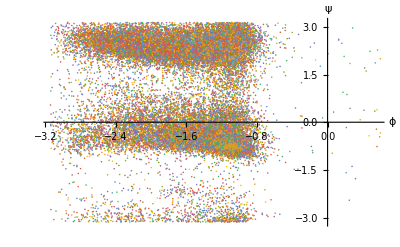

```mathematica
ListPlot[ϕψ,AxesLabel->{"ϕ","ψ"}]
```

The angle ψ can be associated to the curvature on the Cα carbon and on the CO carbon

```mathematica
κψCα=Table[Transpose[{Delete[κ⟦i,1;;;;3⟧,-1],ψ⟦i⟧}],{i,Length[κ]}];
κψCO=Table[Transpose[{κ⟦i,2;;;;3⟧,ψ⟦i⟧}],{i,Length[κ]}];
```

The angle ω can be associated to the curvature on the CO carbon and on the N atom of next residue

```mathematica
κωCO=Table[Transpose[{κ⟦i,2;;;;3⟧,ω⟦i⟧}],{i,Length[κ]}];
κωN=Table[Transpose[{κ⟦i,3;;;;3⟧,ω⟦i⟧}],{i,Length[κ]}];
```

The angle ϕ can be associated to the curvature on the N atom and α carbon

```mathematica
κϕN=Table[Transpose[{κ⟦i,3;;;;3⟧,ϕ⟦i⟧}],{i,Length[κ]}];
κϕCα=Table[Transpose[{κ⟦i,4;;;;3⟧,ϕ⟦i⟧}],{i,Length[κ]}];
```

The pair using 1-5 torsions

```mathematica
κδ1=Table[Transpose[{Delete[κ⟦i,2;;⟧,-1],𝒟⟦i⟧}],{i,Length[κ]}];
κδ=Table[Prepend[Append[κδ1⟦i⟧,Last[κδ1⟦i⟧]],First[κδ1⟦i⟧]],{i,Length[κ]}];
κδN=κδ⟦;;,1;;;;3⟧;
κδCα1=κδ⟦;;,2;;;;3⟧;
κδCα=Table[Append[κδCα1⟦i⟧,Last[κδCα1⟦i⟧]],{i,Length[κδCα1]}];
κδCO1=κδ⟦;;,3;;;;3⟧;
κδCO=Table[Append[κδCO1⟦i⟧,Last[κδCO1⟦i⟧]],{i,Length[κδCO1]}];
```

The pair using 1 - 6 torsions, there are two possible definitions L or R

```mathematica
(* κτ1=Table[Transpose[{κ⟦i,1;;Length[ℛ⟦i⟧]⟧,ℛ⟦i,1;;Length[ℛ⟦i⟧]⟧}],{i,Length[κ]}];
κτ=Table[Append[κτ1⟦i⟧,Last[κτ1⟦i⟧]],{i,Length[κ]}];
*)
```

Filter data to remove empty items

```mathematica
(*list[helix]=Delete[list[helix],itemsdelete1];
list[sheet]=Delete[list[sheet],itemsdelete1];
list[coil]=Delete[list[coil],itemsdelete1];*)
```

Filter helices and sheets to create a scoring system for the κτ list

```mathematica
(*ακτ=Flatten[Table[κτ⟦i,j⟧,{i,1,Length[κτ]},{j,list[helix]⟦i⟧/.range[0]->Nothing}],{1,2}];
βκτ=DeleteCases[Flatten[Table[κτ⟦i,j⟧,{i,1,Length[κτ]},{j,list[sheet]⟦i⟧/.range[0]->Nothing}],{1,2}],List];
γκτ=Flatten[Table[κτ⟦i,j⟧,{i,1,Length[κτ]},{j,list[coil]⟦i⟧}],{1,2}];

{ListPlot[ακτ,PlotStyle->Red],ListPlot[βκτ,PlotStyle->Green],ListPlot[γκτ,PlotStyle->Blue]}
Show[ListPlot[ακτ,PlotStyle->Red,PlotRange->{{0.6,0.9},{-Pi,Pi}}],ListPlot[βκτ,PlotStyle->Green],ListPlot[γκτ,PlotStyle->Blue]]*)
```

Filter helices and sheets to create a scoring system for the κδ list

For N atoms

```mathematica
ακδN=Flatten[Table[κδN⟦i,j⟧,{i,1,Length[κδN]},{j,list[helix]⟦i⟧/.range[0]->Nothing}],{1,2}];
βκδN=DeleteCases[Flatten[Table[κδN⟦i,j⟧,{i,1,Length[κδN]},{j,list[sheet]⟦i⟧/.range[0]->Nothing}],{1,2}],List];
γκδN=Flatten[Table[κδN⟦i,j⟧,{i,1,Length[κδ]},{j,list[coil]⟦i⟧}],{1,2}];
```

For Cα atoms

```mathematica
ακδCα=Flatten[Table[κδCα⟦i,j⟧,{i,1,Length[κδCα]},{j,list[helix]⟦i⟧/.range[0]->Nothing}],{1,2}];
βκδCα=DeleteCases[Flatten[Table[κδCα⟦i,j⟧,{i,1,Length[κδCα]},{j,list[sheet]⟦i⟧/.range[0]->Nothing}],{1,2}],List];
γκδCα=Flatten[Table[κδCα⟦i,j⟧,{i,1,Length[κδCα]},{j,list[coil]⟦i⟧}],{1,2}];
```

For CO atoms

```mathematica
ακδCO=Flatten[Table[κδCO⟦i,j⟧,{i,1,Length[κδCO]},{j,list[helix]⟦i⟧/.range[0]->Nothing}],{1,2}];
βκδCO=DeleteCases[Flatten[Table[κδCO⟦i,j⟧,{i,1,Length[κδCO]},{j,list[sheet]⟦i⟧/.range[0]->Nothing}],{1,2}],List];
γκδCO=Flatten[Table[κδCO⟦i,j⟧,{i,1,Length[κδCO]},{j,list[coil]⟦i⟧}],{1,2}];
```

## Probability distributions

### κδN

```mathematica
temp1=Histogram3D[ακδN]
```

-Graphics3D-

```mathematica
fig1=ListContourPlot[temp1,PlotRange->{{0.6,0.9},{-π,π},{0,6000}},ContourShading->None,ContourStyle->Red,Contours->50]
```

ListContourPlot::arrayerr: must be a valid array.

ListContourPlot[-Graphics3D-,PlotRange→{{0.6,0.9},{-π,π},{0,6000}},ContourShading→None,ContourStyle→RGBColor[1, 0, 0],Contours→50]

```mathematica
temp2=Histogram3D[βκδN]
```

-Graphics3D-

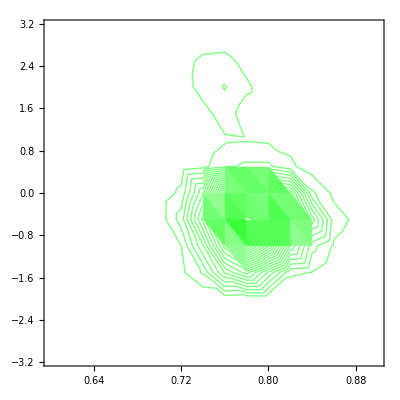

```mathematica
fig2=ListContourPlot[temp2⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,Pi},{0,1500}},ContourShading->None,ContourStyle->Green,Contours->50]
```

```mathematica
temp3=Histogram3D[γκδN]
```

-Graphics3D-

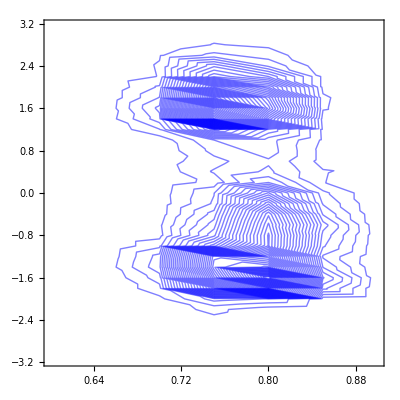

```mathematica
fig3=ListContourPlot[temp3⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,π},{0,1000}},ContourShading->None,ContourStyle->Blue,Contours->50]
```

```mathematica
Show[fig3,fig2,fig1]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,ListContourPlot[-Graphics3D-,PlotRange→{{0.6,0.9},{-π,π},{0,6000}},ContourShading→None,ContourStyle→RGBColor[1, 0, 0],Contours→50]]

```mathematica
κδNregions=Show[
SmoothHistogram3D[ακδN,PlotStyle->Red,PlotRange->{{0.6,0.9},{-π,π},{0,100}},ViewPoint->Above],
SmoothHistogram3D[βκδN,PlotStyle->Green,PlotRange->{{0.6,0.9},{-π,π},{0,100}}],
SmoothHistogram3D[γκδN,PlotStyle->Blue,PlotRange->{{0.6,0.9},{-π,π},{0,100}}]]
```

-Graphics3D-

### κδCα

#### α-helix

Plot the histogram for α helices

```mathematica
hκδCα[histogram]=Histogram3D[ακδCα,{{0.5,1.,0.02},{-π,π,0.2}}]
```

-Graphics3D-

Extract the data from the histogram

```mathematica
hκδCα[grid,xy]=Cases[hκδCα[histogram],Cuboid[x_,y_]->{x,y},{0,∞}];
```

Generate the x and y  grid points (average of the left-right, bottom-top)

```mathematica
hκδCα[grid,x,1]=hκδCα[grid,xy]⟦;;,1,1⟧+hκδCα[grid,xy]⟦;;,2,1⟧;
hκδCα[grid,x,2]=Sort[DeleteDuplicates[hκδCα[grid,x,1]/2.]];
```

```mathematica
Δx=Min[Differences[hκδCα[grid,x,2]]];
hxgrid=Table[x,{x,0.51,1.,Δx}];
```

```mathematica
hκδCα[grid,y,1]=Sort[DeleteDuplicates[(hκδCα[grid,xy]⟦;;,1,2⟧+hκδCα[grid,xy]⟦;;,2,2⟧)/2.]];
```

```mathematica
Δy=Min[Differences[hκδCα[grid,y,1]]];
hygrid=Table[0.1+y,{y,-π,π,Δy}];
```

```mathematica
hxygrid=Tuples[{hxgrid,hygrid}];
```

```mathematica
hxygridbase=Transpose[{hxygrid,Table[0.,{i,Length[hxygrid]}]}];
```

the data

```mathematica
hxygriddata=Transpose[{(hκδCα[grid,xy]⟦;;,1,1;;2⟧+hκδCα[grid,xy]⟦;;,2,1;;2⟧)/2.,hκδCα[grid,xy]⟦;;,2,3⟧}];
```

```mathematica
delete[xx_List,cnd_List]:=DeleteCases[xx,{{x_,y_},z_}/;cnd⟦1⟧-Δx/2<x<cnd⟦1⟧+Δx/2 && cnd⟦2⟧-Δy/2<y<cnd⟦2⟧+Δy/2];
```

```mathematica
hconditions=Table[xy0, {xy0,Table[xx0⟦1⟧,{xx0,hxygriddata}]}];
```

```mathematica
hxygridbase1=hxygridbase;Do[hxygridbase1=delete[hxygridbase1,hconditions⟦i⟧],{i,1,Length[hconditions]}]
```

```mathematica
Clear[hxygriddata1];hxygriddata1=Sort[Join[hxygridbase1,hxygriddata]];
```

```mathematica
hxygriddata2=Table[Flatten[hxygriddata1⟦i⟧],{i,Length[hxygriddata1]}];
```

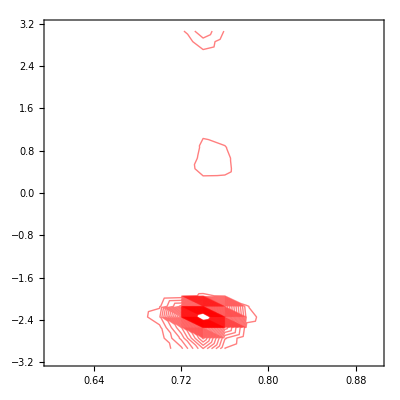

```mathematica
fig1=ListContourPlot[hκδCα[histogram]⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,π},{0,4000}},ContourShading->None,ContourStyle->Red,Contours->50]
```

#### β-sheets

Plot the histogram for α helices

```mathematica
sκδCα[histogram]=Histogram3D[βκδCα,{{0.5,1,0.02},{-π,π,0.2}}]
```

-Graphics3D-

Extract the data from the histogram

```mathematica
sκδCα[grid,xy]=Cases[sκδCα[histogram],Cuboid[x_,y_]->{x,y},{0,∞}];
```

Generate the x and y  grid points (average of the left-right, bottom-top)

```mathematica
sκδCα[grid,x,1]=sκδCα[grid,xy]⟦;;,1,1⟧+sκδCα[grid,xy]⟦;;,2,1⟧;
sκδCα[grid,x,2]=Sort[DeleteDuplicates[sκδCα[grid,x,1]/2.]];
```

```mathematica
Δx=Min[Differences[sκδCα[grid,x,2]]];
sxgrid=Table[x,{x,0.51,1.,Δx}];
```

```mathematica
sκδCα[grid,y,1]=Sort[DeleteDuplicates[(sκδCα[grid,xy]⟦;;,1,2⟧+sκδCα[grid,xy]⟦;;,2,2⟧)/2.]];
```

```mathematica
Δy=Min[Differences[sκδCα[grid,y,1]]];
sygrid=Chop[Table[0.1+y,{y,-π,π,Δy}]];
```

```mathematica
sxygrid=Tuples[{sxgrid,sygrid}];
```

```mathematica
sxygridbase=Transpose[{sxygrid,Table[0.00000000000,{i,Length[sxygrid]}]}];
```

the data

```mathematica
sxygriddata=Transpose[{(sκδCα[grid,xy]⟦;;,1,1;;2⟧+sκδCα[grid,xy]⟦;;,2,1;;2⟧)/2.,sκδCα[grid,xy]⟦;;,2,3⟧}];
```

```mathematica
delete[xx_List,cnd_List]:=DeleteCases[xx,{{x_,y_},z_}/;cnd⟦1⟧-Δx/4<x<cnd⟦1⟧+Δx/4 && cnd⟦2⟧-Δy/4<y<cnd⟦2⟧+Δy/4];
```

```mathematica
sconditions=Table[xy0, {xy0,Table[xx0⟦1⟧,{xx0,sxygriddata}]}];
```

```mathematica
sxygridbase1=sxygridbase;Do[sxygridbase1=delete[sxygridbase1,sconditions⟦i⟧],{i,1,Length[sconditions]}]
```

```mathematica
sxygriddata1=Sort[Join[sxygridbase1,sxygriddata]];
```

```mathematica
sxygriddata2=Table[Flatten[sxygriddata1⟦i⟧],{i,Length[sxygriddata1]}];
```

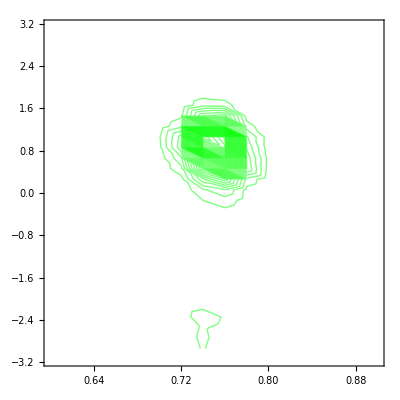

```mathematica
fig1=ListContourPlot[sκδCα[histogram]⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,π},{0,1500}},ContourShading->None,ContourStyle->Green,Contours->50]
```

#### γ-coils

Plot the histogram for α helices

```mathematica
cκδCα[histogram]=Histogram3D[γκδCα,{{0.5,1.,0.02},{-π,π,0.2}}]
```

-Graphics3D-

Extract the data from the histogram

```mathematica
cκδCα[grid,xy]=Cases[cκδCα[histogram],Cuboid[x_,y_]->{x,y},{0,∞}];
```

Generate the x and y  grid points (average of the left-right, bottom-top)

```mathematica
cκδCα[grid,x,1]=cκδCα[grid,xy]⟦;;,1,1⟧+cκδCα[grid,xy]⟦;;,2,1⟧;
cκδCα[grid,x,2]=Sort[DeleteDuplicates[cκδCα[grid,x,1]/2.]];
```

```mathematica
Δx=Min[Differences[cκδCα[grid,x,2]]];
cxgrid=Table[x,{x,0.51,1.,Δx}];
```

```mathematica
cκδCα[grid,y,1]=Sort[DeleteDuplicates[(cκδCα[grid,xy]⟦;;,1,2⟧+cκδCα[grid,xy]⟦;;,2,2⟧)/2.]];
```

```mathematica
Δy=Min[Differences[cκδCα[grid,y,1]]];
cygrid=Chop[Table[y+0.1,{y,-π,π,Δy}]];
```

```mathematica
cxygrid=Tuples[{cxgrid,cygrid}];
```

```mathematica
cxygridbase=Transpose[{cxygrid,Table[0.00000000000,{i,Length[cxygrid]}]}];
```

the data

```mathematica
cxygriddata=Transpose[{(cκδCα[grid,xy]⟦;;,1,1;;2⟧+cκδCα[grid,xy]⟦;;,2,1;;2⟧)/2.,cκδCα[grid,xy]⟦;;,2,3⟧}];
```

```mathematica
delete[xx_List,cnd_List]:=DeleteCases[xx,{{x_,y_},z_}/;cnd⟦1⟧-Δx/4<x<cnd⟦1⟧+Δx/4 && cnd⟦2⟧-Δy/4<y<cnd⟦2⟧+Δy/4];
```

```mathematica
cconditions=Table[xy0, {xy0,Table[xx0⟦1⟧,{xx0,cxygriddata}]}];
```

```mathematica
cxygridbase1=cxygridbase;Do[cxygridbase1=delete[cxygridbase1,cconditions⟦i⟧],{i,1,Length[cconditions]}]
```

```mathematica
cxygriddata1=Sort[Join[cxygridbase1,cxygriddata]];
```

```mathematica
cxygriddata2=Table[Flatten[cxygriddata1⟦i⟧],{i,Length[cxygriddata1]}];
```

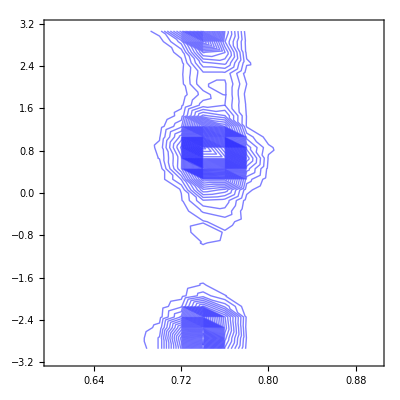

```mathematica
fig1=ListContourPlot[cκδCα[histogram]⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,π},{0,1000}},ContourShading->None,ContourStyle->Blue,Contours->50]
```

#### all data

Normalization of the data

```mathematica
nxy=hxygriddata1⟦;;,2⟧+sxygriddata1⟦;;,2⟧+cxygriddata1⟦;;,2⟧;
```

```mathematica
norm=nxy/.{0.->c};
```

```mathematica
phsc=Table[{hxygriddata1⟦i,1⟧,hxygriddata1⟦i,2⟧/norm⟦i⟧,sxygriddata1⟦i,2⟧/norm⟦i⟧,cxygriddata1⟦i,2⟧/norm⟦i⟧},{i,Length[hxygriddata1]}];
```

Export the produced data to save time avoiding the full evaluation

```mathematica
phscexport=Table[Flatten[{hxygriddata1⟦i,1⟧,hxygriddata1⟦i,2⟧/norm⟦i⟧,sxygriddata1⟦i,2⟧/norm⟦i⟧,cxygriddata1⟦i,2⟧/norm⟦i⟧}],{i,Length[hxygriddata1]}];
```

```mathematica
Export[ToString[NotebookDirectory[]<>"probability_hsc_prot_186.dat"],phscexport,"Table"];
```

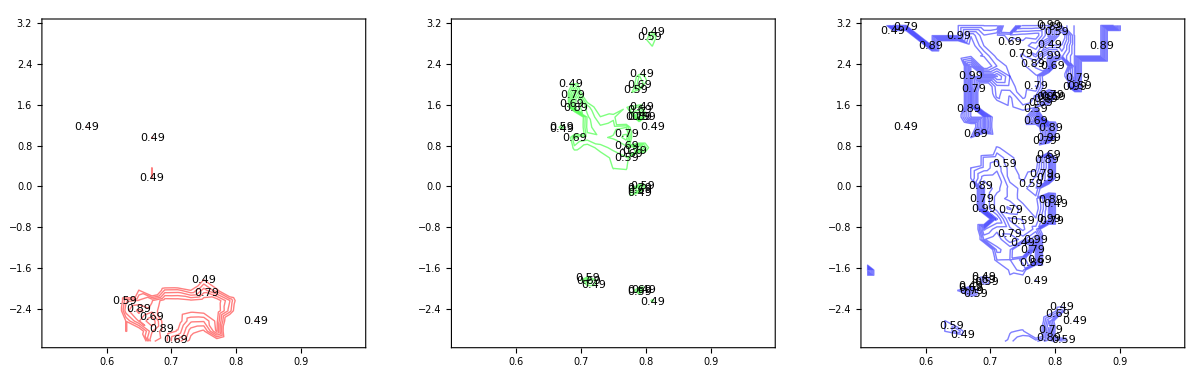

```mathematica
congra=GraphicsRow[{ListContourPlot[Table[Flatten[phsc⟦i,1;;2⟧],{i,Length[phsc]}],PlotRange->{0,2},Contours->Table[z,{z,0.49,0.99,0.1}],ContourStyle->Red,ContourShading->False,ContourLabels->True,PlotTheme->"Detailed"],ListContourPlot[Table[Flatten[phsc⟦i,1;;3;;2⟧],{i,Length[phsc]}],PlotRange->{0,2},Contours->Table[z,{z,0.49,0.99,0.1}],ContourStyle->Green,ContourShading->False,ContourLabels->True,PlotTheme->"Detailed"],ListContourPlot[Table[Flatten[phsc⟦i,1;;4;;3⟧],{i,Length[phsc]}],PlotRange->{0,2},Contours->Table[z,{z,0.49,0.99,0.1}],ContourStyle->Blue,ContourShading->False,ContourLabels->True,PlotTheme->"Detailed"]}]
```

```mathematica
Show[congra,ImageSize->Full]
```

-Graphics-

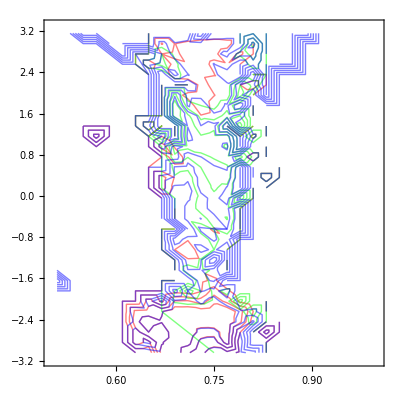

```mathematica
Show[ListPlot3D[Table[Flatten[phsc⟦i,1;;2⟧],{i,Length[phsc]}],PlotRange->{0,1.2},PlotStyle->Red,ViewPoint->Above],ListPlot3D[Table[Flatten[phsc⟦i,1;;3;;2⟧],{i,Length[phsc]}],PlotRange->{0,1.2},PlotStyle->Green],ListPlot3D[Table[Flatten[phsc⟦i,1;;4;;3⟧],{i,Length[phsc]}],PlotRange->{0,1.2},PlotStyle->Blue]]
```

-Graphics3D-

```mathematica
phinter=Interpolation[phsc⟦;;,1;;2⟧,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
psinter=Interpolation[phsc⟦;;,1;;3;;2⟧,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
pcinter=Interpolation[phsc⟦;;,1;;4;;3⟧,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Show[Plot3D[phinter[x,y],{x,0.51,0.9899999999999978},{y,-3.041592653589793,3.158407346410199},PlotRange->{0,1.2},PlotStyle->Red,ViewPoint->Above],Plot3D[psinter[x,y],{x,0.51,0.9899999999999978},{y,-3.041592653589793,3.158407346410199},PlotRange->{0,1.2},PlotStyle->Green],Plot3D[pcinter[x,y],{x,0.51,0.9899999999999978},{y,-3.041592653589793,3.158407346410199},PlotRange->{0,1.2},PlotStyle->Blue]]
```

-Graphics3D-

### κδCO

```mathematica
temp1=Histogram3D[ακδCO]
```

-Graphics3D-

```mathematica
fig1=ListContourPlot[temp1⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,Pi},{0,8000}},ContourShading->None,ContourStyle->Red,Contours->50]
```

Outer::normal: Nonatomic expression expected at position 2 in Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«6»}].

MapThread::mptd: Object Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«6»}] at position {2, 1} in MapThread[Append,{Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«6»}],{{Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«27»,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«6»}}},2] has only 0 of required 2 dimensions.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Append,{Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«6»}],{{Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«29»,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«6»}}},2.].

ListContourPlot::gmat: {{Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«3»,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«6»}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel}},PlotRange→{{0.6,0.9},{-π,π},{0,8000}},ContourShading→None,ContourStyle→RGBColor[1, 0, 0],Contours→50]

```mathematica
temp2=Histogram3D[βκδCO]
```

-Graphics3D-

```mathematica
fig2=ListContourPlot[temp2⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,Pi},{0,200}},ContourShading->None,ContourStyle->Green,Contours->50]
```

Outer::normal: Nonatomic expression expected at position 2 in Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«45»}].

MapThread::mptd: Object Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«45»}] at position {2, 1} in MapThread[Append,{Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«45»}],{{Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«28»,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«45»}}},2] has only 0 of required 2 dimensions.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Append,{Outer[List,1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«45»}],{{Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«29»,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«45»}}},2.].

ListContourPlot::gmat: {{Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«3»,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,Graphics3DLabel,«45»}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel}},PlotRange→{{0.6,0.9},{-π,π},{0,200}},ContourShading→None,ContourStyle→RGBColor[0, 1, 0],Contours→50]

```mathematica
temp3=Histogram3D[γκδCO]
```

-Graphics3D-

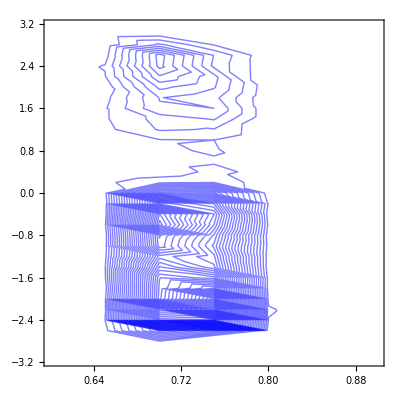

```mathematica
fig3=ListContourPlot[temp3⟦1,2,2,2,;;,1,2,2⟧,PlotRange->{{0.6,0.9},{-π,π},{0,1000}},ContourShading->None,ContourStyle->Blue,Contours->50]
```

```mathematica
Histogram3D[{ακδCO,βκδCO,γκδCO}]
```

-Graphics3D-

```mathematica
Show[fig3,fig2,fig1]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListContourPlot[{{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel}},PlotRange→{{0.6,0.9},{-π,π},{0,200}},ContourShading→None,ContourStyle→RGBColor[0, 1, 0],Contours→50],ListContourPlot[{{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel},{Graphics3DLabel}},PlotRange→{{0.6,0.9},{-π,π},{0,8000}},ContourShading→None,ContourStyle→RGBColor[1, 0, 0],Contours→50]]

```mathematica
κδCαregions=Show[
SmoothHistogram3D[ακδCO,PlotStyle->Red,PlotRange->{{0.6,0.9},{-π,π},{0,100}},ViewPoint->Above],
SmoothHistogram3D[βκδCO,PlotStyle->Green,PlotRange->{{0.6,0.9},{-π,π},{0,100}}],
SmoothHistogram3D[γκδCO,PlotStyle->Blue,PlotRange->{{0.6,0.9},{-π,π},{0,100}}]]
```

-Graphics3D-

## Figures

```mathematica
Spacer
```

Spacer

FIGURES HISTOGRAMS

```mathematica
hακδCαnormalized[histogram]=Histogram3D[ακδCα,{{0.6,0.9,0.02},{-π,π,0.2}},Probability,PlotTheme->"Monochrome",Ticks->{Automatic,{{-π,1},{-π/2,"-0.5"},0,{π/2,"0.5"},{π,1}}},TicksStyle->Directive[GrayLevel[0.37],9], ChartStyle->Directive[EdgeForm[Black],Gray],AxesStyle->Black,AxesLabel->{Style["κ",FontFamily->"Times New Roman",14],Style["  τ/π",FontFamily->"Times New Roman",14],Style["P_(H,  α) ",FontFamily->"Times New Roman",14]},AspectRatio->1,Boxed->True];
```

```mathematica
hβκδCαnormalized[histogram]=Histogram3D[βκδCα,{{0.6,0.9,0.02},{-π,π,0.2}},Probability,PlotTheme->"Monochrome",Ticks->{Automatic,{{-π,1},{-π/2,"-0.5"},0,{π/2,"0.5"},{π,1}}},TicksStyle->Directive[GrayLevel[0.37],9], ChartStyle->Directive[EdgeForm[Black],Gray],AxesStyle->Black,AxesLabel->{Style["κ",FontFamily->"Times New Roman",14],Style["  τ/π",FontFamily->"Times New Roman",14],Style["P_(H,  β) ",FontFamily->"Times New Roman",14]},AspectRatio->1];
```

```mathematica
hγκδCαnormalized[histogram]=Histogram3D[γκδCα,{{0.6,0.9,0.02},{-π,π,0.2}},Probability,PlotTheme->"Monochrome",Ticks->{Automatic,{{-π,1},{-π/2,"-0.5"},0,{π/2,"0.5"},{π,1}}},TicksStyle->Directive[GrayLevel[0.37],9], ChartStyle->Directive[EdgeForm[Black],Gray],AxesStyle->Black,AxesLabel->{Style["κ",FontFamily->"Times New Roman",14],Style["  τ/π",FontFamily->"Times New Roman",14],Style["P_(H,  γ) ",FontFamily->"Times New Roman",14]},AspectRatio->1];
```

```mathematica
figall=GraphicsRow[{hακδCαnormalized[histogram],hβκδCαnormalized[histogram],hγκδCαnormalized[histogram]}]
```

-Graphics-

```mathematica
Show[figall,ImageSize->Large]
```

-Graphics-

```mathematica
Export["histograms.pdf",Show[figall,ImageSize->Large]]
```

histograms.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["histograms.pdf"]]]
```

```mathematica
RankedMax[cxygriddata1⟦;;,2⟧,2]
```

693.